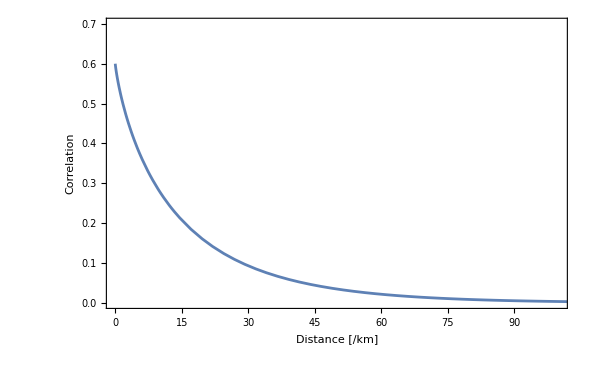

```mathematica
v:=2.4
a:=v
be :=0.95
b[l_]:=(t[l]*(v-1)+1+e)
c[l_]:=√(t[l]*(v^2-1))
z[l_]:=√((a+b[l])^2-4*c[l]^2)
f[E_]:=((E+1)/2)Log2[((E+1)/2)]-((E-1)/2)Log2[((E-1)/2)]
E1[l_]:=1/2(z[l]+(b[l]-a))
E2[l_]:=1/2(z[l]-(b[l]-a))
E3[l_]:=√(a(a-c[l]^2/b[l]))
fE1[l_]:=f[E1[l]]
fE2[l_]:=f[E2[l]]
fE3[l_]:=f[E3[l]]
fE12[l_]:=(fE1[l]+fE2[l])
χ1[l_]:=fE12[l] - fE3[l]
SNR[l_]:= (t[l] * (v-1))/(1+e)
IAB[l_]:=1/2 Log2[1+SNR[l]]
r[l_]:=(be*IAB[l] -χ1[l])
r2[l_]:=(2*10^6)* r[l]
e:=10^-10
(*t[l_]:=10^(-0.025*l)*)
t[l_]:=1/10^(0.02*l)
Plot[{r[l]},{l,0,120},Frame->True,FrameLabel->{"Distance  [/km]","Correlation"},LabelStyle->{Directive[Black,20]},PlotStyle->{Line},PlotRange->{{0,100},{0,0.7}}]
```